This notebook shows magnetometery calculations using the method outlined in the paper “Exact steady state of perturbed open quantum systems”: https://arxiv.org/abs/2501.06134. See the paper for detailed explanation of the technique. 

The code generates Fig. 4 in the paper.

If you use this work for research, we would appreciate citing the paper.

- Omar Nagib* and Thad G. Walker**

*onagib@wisc.edu
**tgwalker@wisc.edu

Install the packages MaTeX and CustomTicks to properly generate the figures:

```mathematica
<<MaTeX`
```

```mathematica
Get["CustomTicks`"]
```

************************************************************************************

Notational definitions

vectorization:  want to represent the N×N density matrix as a N^2 column vector

let v(A)=|A)=∑_ij A_ij i⊗j=∑_ij A_ij i j
Example:  two-level atom ρ=ρ_ee | ρ_eg
ρ_ge | ρ_gg->v(ρ)=ρ_ee
ρ_eg
ρ_ge
ρ_gg

```mathematica
<<Notation`
```

```mathematica
vec[A_]:=Flatten[A]
```

Define ⊗ as Kronecker product of x and y:

```mathematica
ClearAll[CircleTimes];

CircleTimes[x_,y_]:=KroneckerProduct[x,y];
```

Define the symbol 𝕀_n as the n by n Identity matrix:

```mathematica
ClearAll[𝕀];
Subscript[𝕀,n_]:=IdentityMatrix[n];
```

Define ᵀ as transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"ᵀ"]]⟹ParsedBoxWrapper[RowBox[{"Transpose","[",x,"]"}]]];
```

Define † as conjugate transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"†"]]⟹ParsedBoxWrapper[RowBox[{"ConjugateTranspose","[",x,"]"}]]];
```

Define | ⟩ as a column vector, a ket:

```mathematica
ClearAll[Ket];

Ket[v_List]:=Transpose[{Flatten[v]}];
```

Define * as conjugate transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"*"]]⟹ParsedBoxWrapper[RowBox[{"Conjugate","[",x,"]"}]]];
```

Define * as conjugate transpose:

```mathematica
Notation[ParsedBoxWrapper[SuperscriptBox[x_,"*"]]⟹ParsedBoxWrapper[RowBox[{"Conjugate","[",x,"]"}]]];
```

************************************************************************************
Constructing the angular momentum operators:

This section creates angmom[J]={J_x,J_y,J_z} which gives the angular momentum matrices for a J-spin system.
This will be useful for constructing the total Hamiltonian in the next section. For derivations of the definitions to be used below, consult any standard quantum mechanics textbook on angular momentum.

```mathematica
angmom[jqn_]:=With[{jp=DiagonalMatrix[Table[Sqrt[jqn(jqn+1)-mqn(mqn+1)],{mqn,jqn-1,-jqn,-1}],1]},{(jp+jpᵀ)/2,(jp-jpᵀ)/(2I),DiagonalMatrix[Range[jqn,-jqn,-1]]}];
```

************************************************************************************
Constructing the unperturbed Hamiltonian and the Lindblad operators
-Graphics-
-Graphics-

prep[Ω_z] is a module that constructs the Hamiltonian H_0 for a given f_z=Ω_z/2π in KHz unit:

```mathematica
(*f0 is the fz=Ωz/2π*)
```

```mathematica
prep[f0_]:=
Module[{},
𝓈=angmom[1/2](*Define electron spin*);𝒾=angmom[iqn=3/2](*Nuclear spin*);gi=2 iqn+1;
𝓈=Map[#⊗Subscript[𝕀, gi]&,𝓈];𝒾=Map[Subscript[𝕀, 2]⊗#&,𝒾];(*tensor product of the two spin spaces*)
𝒻=𝓈+𝒾;(*total spin*)
H=6835000./(iqn+1/2)Sum[𝓈⟦p⟧.𝒾⟦p⟧,{p,3}]+f0  𝓈⟦3⟧;(*Define the Hamiltonian Subscript[H, 0], where ω0=6835000 is the Rb87 hyperfine splitting in units of GHz*){eH,uH}=Eigensystem[H];in=Ordering[-eH];eH=eH⟦in⟧;uH=uH⟦in⟧;
H=SuperStar[uH].H.uHᵀ;
𝓈=Map[SuperStar[uH].#.uHᵀ&,𝓈];
𝒾=Map[SuperStar[uH].#.uHᵀ&,𝒾];𝒻=Map[SuperStar[uH].#.uHᵀ&,𝒻];
]
```

Initialize H_0 for f_z=1 KHz

```mathematica
prep[1];
```

Next, let’s construct the Lindbald operators (the units are in KHz): 
-Graphics-

```mathematica
L1=√Γ 𝓈[[1]];
L2=√Γ 𝓈[[2]];
L3=√Γ 𝓈[[3]];
L4=√R(𝓈[[1]]+I 𝓈[[2]]);
L5=√R 𝓈[[3]];
```

Now let’s construct the Lindbaldian:
-Graphics-

```mathematica
ℒ=   -2π I(H⊗Subscript[𝕀, Length[H]]-Subscript[𝕀, Length[H]]⊗Hᵀ)+( L1⊗SuperStar[L1]-1/2 SuperDagger[L1].L1⊗Subscript[𝕀, Length[H]]-1/2 Subscript[𝕀, Length[H]]⊗L1ᵀ.SuperStar[L1])+( L2⊗SuperStar[L2]-1/2 SuperDagger[L2].L2⊗Subscript[𝕀, Length[H]]-1/2 Subscript[𝕀, Length[H]]⊗L2ᵀ.SuperStar[L2])+( L3⊗SuperStar[L3]-1/2 SuperDagger[L3].L3⊗Subscript[𝕀, Length[H]]-1/2 Subscript[𝕀, Length[H]]⊗L3ᵀ.SuperStar[L3])+( L4⊗SuperStar[L4]-1/2 SuperDagger[L4].L4⊗Subscript[𝕀, Length[H]]-1/2 Subscript[𝕀, Length[H]]⊗L4ᵀ.SuperStar[L4])+( L5⊗SuperStar[L5]-1/2 SuperDagger[L5].L5⊗Subscript[𝕀, Length[H]]-1/2 Subscript[𝕀, Length[H]]⊗L5ᵀ.SuperStar[L5]);
```

Initialize ℒ for a given system parameters and find the steady state:

```mathematica
ℒ0=ℒ/.{R->2., Γ->0.1};(*R=2/ms Γ=0.1/ms*)
ρnullspace=Flatten[NullSpace[ℒ0]];
Traceρnullspace=vec[Subscript[𝕀, Length[H]]].ρnullspace;
ρ∞=ρnullspace/Traceρnullspace;
```

***************************************************************************************************
Magnetometer steady state response by the present method:

-Graphics-

Now construct the generalized inverse 

ℒ_0^-=∑_(g≠0) 1/g R_g⊗(L^T)_g 
To construct ℒ_0^- efficiently, we denote R_-=(R_1 R_2...R_(N-1)), where R_g is the column right eigenvector with length N, and L_-=(L_1 L_2...L_(N-1)), where L_g is the column left eigenvector with length N. Let G_-=(g_1 g_2... g_(N-1)) be the list of eigenvalues. The minus subscript in R_-, L_-, and G_- denotes that we are excluding the zero eigenvalues and vectors from these objects.  An equivalent way to rewrite ℒ_0^- is then

ℒ_0^-=(1/(G_-)R_- ).(L_-)^T (normal version)

Here 1/(G_-)R_- denotes the elementwise division: (R_1/g_1 R_2/g_2...(R_(N-1))/(g_(N-1))) while the dot denotes normal matrix multiplication. In Mathematica, the output of eigensystem are rows not columns. Therefore, in Mathematica it is be given by

ℒ_0^-=(1/(G_-)R_- )^T.L_-   (Mathematica version)

Method 2) Using an inverse identity:

We note that ℒ_0^- can be directly constructed as

ℒ_0^-=(ℒ_0+ (R_0 L_0^T))^-1-R_0 L_0^T

i.e., add the nullspace projector P_0=R_0 L_0^T, take the inverse, and then subtract P_0 again. This completely avoids explicit diagonalization and construction of right/left eigenvectors.

```mathematica
P0=SparseArray[KroneckerProduct[ρ∞,Transpose[vec[Subscript[𝕀, Length[H]]]]]];
```

```mathematica
ℒ0minus=Inverse[ℒ0+P0]-P0;
```

```mathematica
(*xsucc=LinearSolve[ℒSparse0,SparseP0];*)
```

Construct the auxiliary Lindbladian ℒ_1:

```mathematica
ℒ1=-I(𝓈[[2]]⊗Subscript[𝕀, Length[H]]-Subscript[𝕀, Length[H]]⊗Transpose[𝓈[[2]]]);
```

Now diagonalize the auxiliary problem to find the Propagator:

```mathematica
{λ,rλ}=Eigensystem[ℒ0minus.ℒ1];
```

```mathematica
Lλ=PseudoInverse[Transpose[rλ]];
```

The steady state as a function of Ω_y then would be given by:

 ρ_Ωy=(∑_λ 1/(1+λ Ωy)r_λ⊗l_λ)ρ_0, which can be rewritten as

ρ_Ωy={(1/(1+Ωy Λ)r)^T.l}.ρ_0

where r=(r_1 r_2...r_N) is the right eigenvectors of ℒ_0^-ℒ_1 and l=(l_1 l_2...l_N) are the left eigenvectors and Λ=(λ_1 λ_2... λ_N) are the eigenvalues. 1/(1+Ωy Λ)r is an elementwise division between Λ and r while the dot denotes matrix multiplication:

```mathematica
ρΩy[Ωy_]:=(Transpose[(1/(1+Ωy λ))rλ].Lλ).ρ∞;
```

Or  using the identity 1/(I+A)=I-A/(1+A) on ρ_Ωy. We get 

ρ_Ωy=ρ_0-{((Ωy Λ)/(1+Ωy Λ)r)^T.l}.ρ_0

Note that we can exclude all the nullspaces/zero eigenvectors/values in the second term, without affecting ρ_Ωy. 

In the present case the non-zero eigenvalues run from 1 to 26; the rest are zero.

```mathematica
ρΩy2[Ωy_]:=ρ∞-(Transpose[(Ωy λ[[1;;26]])/(1+Ωy λ[[1;;26]])rλ[[1;;26]]].Lλ[[1;;26]]).ρ∞;
```

Compare the present approach with the exact solution from the Bloch equations:
-Graphics-

Let’s plot S_x by the present method and the solution to the Bloch Eqs:

<S_x> = 1/2(R Ω_y)/(Ω^2+(Γ+R)^2) with Ω^2=(Ω^2)_z+(Ω^2)_y=(2π 1)^2+(Ω^2)_y and  (Γ+R)^2=(2+0.1)^2:

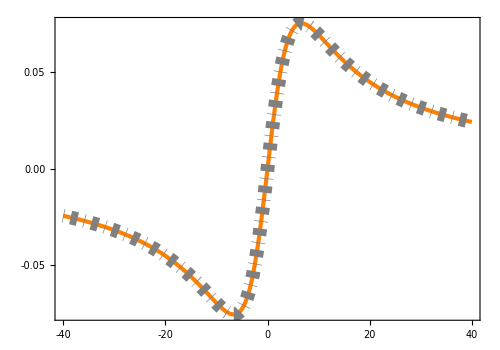

```mathematica
SxOmegaPlot=Plot[{Re[vec[𝓈⟦1⟧].ρΩy[Ωy]],1/2(Ωy 2)/((2π 1)^2+(Ωy)^2+(2+.1)^2)},{Ωy,-40,40},FrameLabel->{MaTeX["\\Omega_y \ (\\text{rad/ms})",Magnification->3],MaTeX["\\langle S_x \\rangle",Magnification->3]},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],FrameTicks->{{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&},{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&}},GridLines->None,ImageSize->500,PlotRange->All,Axes->False,PlotLegends->Placed[LineLegend[{"",""},LegendMarkerSize->{0,3}],{0.27,0.8}],PlotStyle->{Directive[Orange,AbsoluteThickness[3]],Directive[Gray,DotDashed,AbsoluteThickness[10]]},LabelStyle->{FontSize->21,FontFamily->"Times New Roman"},AspectRatio->0.7]
```

Now, let’s compute dS_x/dΩ_y exactly using the present approach (by differentiating the propagator, which is an explicit function of Ω_y) and compare it with the Bloch equations:

```mathematica
ρΩy3=(Transpose[(1/(1+Ωy λ))rλ].Lλ).ρ∞;
```

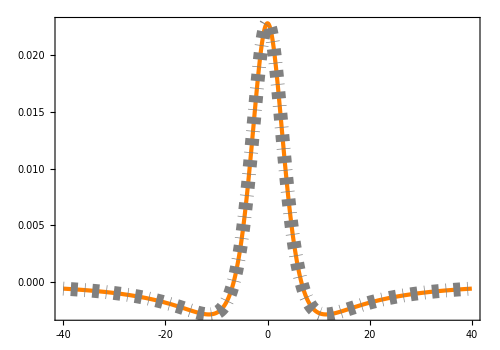

```mathematica
DSxOmegaPlot=Plot[{Evaluate[Re[vec[𝓈⟦1⟧].D[ρΩy3,Ωy]]],Evaluate[D[1/2(Ωy 2)/((2π 1)^2+(Ωy)^2+(2+.1)^2),Ωy]]},{Ωy,-40,40},FrameLabel->{MaTeX["\\Omega_y \ (\\text{rad/ms})",Magnification->3],MaTeX["d\\langle S_x \\rangle/d\\Omega_y",Magnification->3]},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],FrameTicks->{{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&},{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&}},GridLines->None,ImageSize->500,PlotRange->All,Axes->False,PlotLegends->Placed[LineLegend[{"",""},LegendMarkerSize->{0,3}],{0.25,0.8}],PlotStyle->{Directive[Orange,AbsoluteThickness[3]],Directive[Gray,DotDashed,AbsoluteThickness[10]]},LabelStyle->{FontSize->22,FontFamily->"Times New Roman"},AspectRatio->0.7]
```

-Graphics-

Below we compute the magnetometer’s sensitivity as outlined in the text above:

```mathematica
ℒΩ=-I(𝓈[[2]]⊗Subscript[𝕀, Length[H]]-Subscript[𝕀, Length[H]]⊗Transpose[𝓈[[2]]]);(*Lindbladian for Ωy*)
```

```mathematica
(*Lindbladian for optical pumping*)
```

```mathematica
ℒR=(( L4⊗SuperStar[L4]-1/2 SuperDagger[L4].L4⊗Subscript[𝕀, Length[H]]-1/2 Subscript[𝕀, Length[H]]⊗L4ᵀ.SuperStar[L4])+( L5⊗SuperStar[L5]-1/2 SuperDagger[L5].L5⊗Subscript[𝕀, Length[H]]-1/2 Subscript[𝕀, Length[H]]⊗L5ᵀ.SuperStar[L5]))/.{R->1};
```

```mathematica
(*Lindbladian when both Ωy=R=0*)
```

```mathematica
ℒ00=ℒ/.{R->0., Γ->0.1};
ρnullspace00=Flatten[NullSpace[ℒ00]];
Traceρnullspace00=vec[Subscript[𝕀, Length[H]]].ρnullspace00;
ρ00=ρnullspace00/Traceρnullspace00;
```

Now diagonalize ℒ00:

```mathematica
{egnv00,Regnvec00}=Eigensystem[ℒ00];
```

```mathematica
Legnvec00=PseudoInverse[Transpose[Regnvec00]];
```

Now construct the generalized inverse

```mathematica
ℒ00minus=Transpose[(1/egnv00[[1;;-2]])Regnvec00[[1;;-2,All]]].Legnvec00[[1;;-2,All]];
```

```mathematica
(*Solve the auxiliary problem ℒ00minus.ℒR*)
```

```mathematica
{λR,rλR}=Eigensystem[ℒ00minus.ℒR];
```

```mathematica
LλR=PseudoInverse[Transpose[rλR]];
```

Use:

∂_Ω ρ(R,0)=-𝕀/(𝕀+R ℒ_0^-ℒ_R)ℒ_0^-ℒ_Ω ρ(R,0)=-𝕀/(𝕀+R ℒ_0^-ℒ_R)ℒ_0^-ℒ_Ω_2 𝕀/(𝕀+R G_0^-G_R)ρ_00
where ℒ_0^-ℒ_R is diagonalized here:

```mathematica
res=Sum[vec[𝓈⟦1⟧].rλR⟦i⟧ -1/(1+R λR⟦i⟧)LλR⟦i⟧.ℒ00minus.ℒΩ.rλR⟦j⟧ 1/(1+R λR⟦j⟧)LλR⟦j⟧.ρ00,{i,64},{j,64}];
```

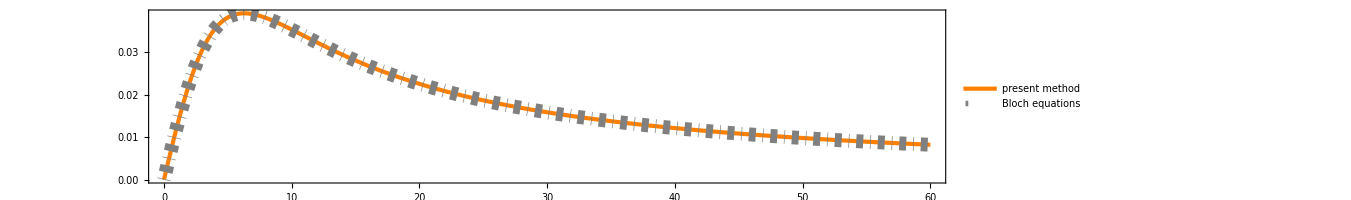

```mathematica
DSxOmegaRPlot=Plot[{Re@res,Evaluate[D[1/2(Ωy R)/((2π 1)^2+Ωy^2+(R+.1)^2),Ωy]/.Ωy->0]},{R,0,60},FrameLabel->{MaTeX["R \ (\\text{1/ms})",Magnification->3],MaTeX["d\\langle S_x \\rangle/d\\Omega_y",Magnification->3]},Frame->True,FrameStyle->Directive[GrayLevel[0],30,FontFamily->"Times New Roman",AbsoluteThickness[1.0]],FrameTicks->{{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&},{LinTicks,LinTicks[#1,#2,ShowTickLabels->False]&}},GridLines->None,ImageSize->1000,PlotRange->All,Axes->False,PlotLegends->Placed[LineLegend[{"present method","Bloch equations"},LegendMarkerSize->{40,10}],{0.7,0.7}],PlotStyle->{Directive[Orange,AbsoluteThickness[3]],Directive[Gray,DotDashed,AbsoluteThickness[10]]},LabelStyle->{FontSize->30,FontFamily->"Times New Roman"},AspectRatio->0.2]
```

Now analytically find R that maximizes the sensitivity using the present approach, without sampling/discretization:

Analytically find the maximum:

```mathematica
Highlighted[FindMaximum[Re[res],R]]
```

FindMaximum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient increase in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.0391605,{R→6.28398}}

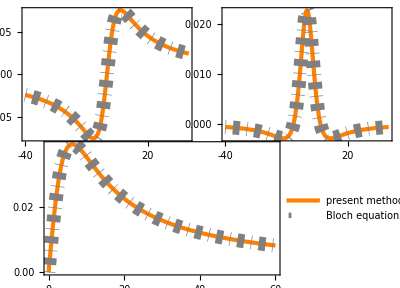

```mathematica
GraphicsGrid[{{SxOmegaPlot,DSxOmegaPlot},{DSxOmegaRPlot,SpanFromLeft}},ImageSize->Full,Spacings->{0,-50},Alignment->Center,ImagePadding->{{Automatic,Automatic},{125,Automatic}}]
```